Andrea Halenkamp

```mathematica
x''[t]+x'[t]+5*x[t]=0
```

```mathematica
Clear[x,xold,y,t,Δt,solution,f]
solution={};

t0=0;
tmax=6;
steps=25;
Δt=(tmax-t0)/steps; 
f[x_,y_]:=-y-5*x;
t=0.0;  
x=1.0;
y=2.0;
AppendTo[solution,{t,x,y}];

Do[
xold=x;
x=xold+y*Δt;
y=y+Δt*f[xold,y];
t=t+Δt;
AppendTo[solution,{t,x,y}];
,{steps}];

ListPointPlot3D[Table[{solution[[i,1]],solution[[i,2]],solution[[i,3]]},{i,steps+1}]]
```

-Graphics3D-

## Graph x vs. t:

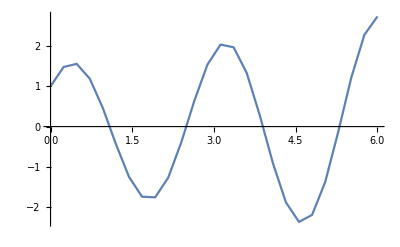

```mathematica
ListLinePlot[Table[{solution[[i,1]],solution[[i,2]]},{i,steps+1}]]
```

## Graph y vs. t:

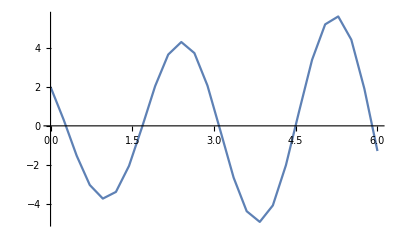

```mathematica
ListLinePlot[Table[{solution[[i,1]],solution[[i,3]]},{i,steps+1}]]
```

## Graph y vs. x (phase plane):

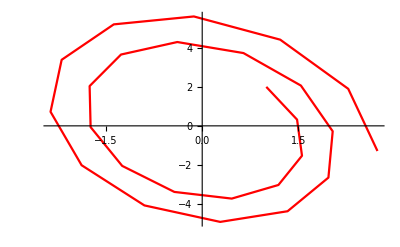

```mathematica
plot2=ListLinePlot[Table[{solution[[i,2]],solution[[i,3]]},{i,steps+1}],PlotStyle->Red]
```

## Graph Vector Field (y vs. x) :

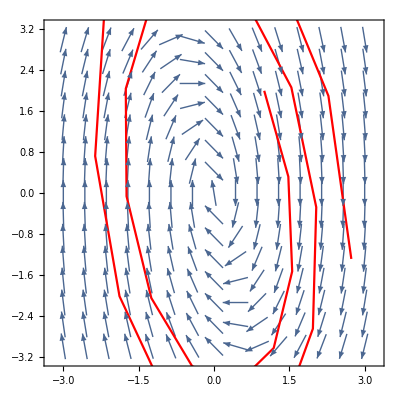

```mathematica
plot1=VectorPlot[{y,-y-5*x},{x,-3,3},{y,-3,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}];
Show[plot1,plot2]
```

```mathematica
x''[t]+2*x'[t]+x[t]=0
```

```mathematica
Clear[x,xold,y,t,Δt,solution,f]
solution={};

t0=0;
tmax=10;
steps=25;
Δt=(tmax-t0)/steps; 
f[x_,y_]:=-2y-x;
t=0.0;  
x=1.0;
y=2.0;
AppendTo[solution,{t,x,y}];

Do[
xold=x;
x=xold+y*Δt;
y=y+Δt*f[xold,y];
t=t+Δt;
AppendTo[solution,{t,x,y}];
,{steps}];

ListPointPlot3D[Table[{solution[[i,1]],solution[[i,2]],solution[[i,3]]},{i,steps+1}]]
```

-Graphics3D-

## Graph x vs. t:

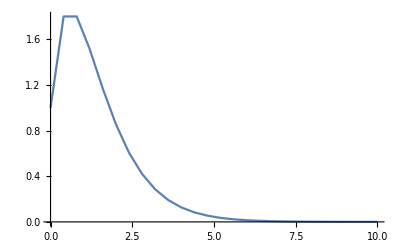

```mathematica
ListLinePlot[Table[{solution[[i,1]],solution[[i,2]]},{i,steps+1}]]
```

## Graph y vs. t:

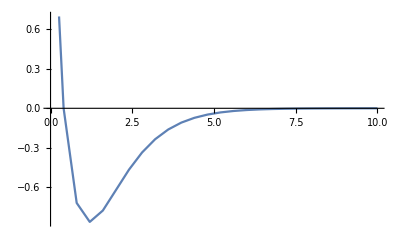

```mathematica
ListLinePlot[Table[{solution[[i,1]],solution[[i,3]]},{i,steps+1}]]
```

## Graph y vs. x (phase plane):

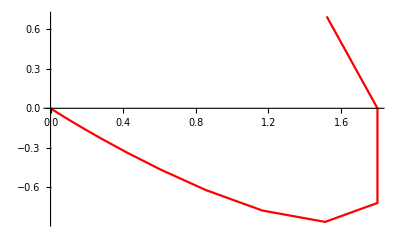

```mathematica
plot2=ListLinePlot[Table[{solution[[i,2]],solution[[i,3]]},{i,steps+1}],PlotStyle->Red]
```

## Graph Vector Field (y vs. x) :

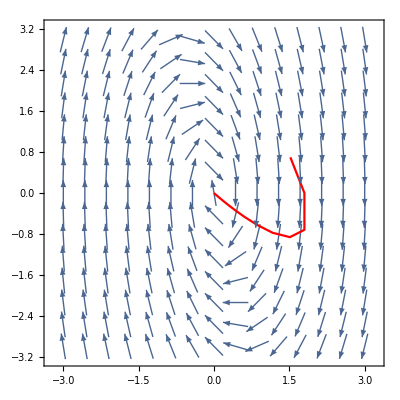

```mathematica
plot1=VectorPlot[{y,-y-5*x},{x,-3,3},{y,-3,3},Axes->True,Frame->True,VectorScale->{Small,Automatic,None}];
Show[plot1,plot2]
```